```mathematica
FreeAdd[sfA_,sfB_,m_:50,n_:30]:=Quiet[
Module[{GAB,GABD,GABDD,xia,xib,Apts,Bpts,sIptsA,sIptsB,sIpts,sgpts,gpts,ret,AB,a,b},
GAB[y_]:=StieljesInverseFunction[sfA,y]+StieljesInverseFunction[sfB,y]-1/y//First;
GABD[y_]:=StieljesInverseFunctionD[sfA,y]+StieljesInverseFunctionD[sfB,y]+1/y^2//Re//First;
GABDD[y_]:=StieljesInverseFunctionD[2][sfA,y]+StieljesInverseFunctionD[2][sfB,y]-1/y^3//Re//First;
{xia,xib}={NewtonMethod[GABD,GABDD,-.1],NewtonMethod[GABD,GABDD,.1]};
{a,b}=GAB/@{xia,xib}//Re;
(Apts=MapFromInterval[sfA//First,Table[Points[Circle[0,r],n],{r,1/(n-1),1.,1/(n-1)}]//Flatten//CircleToInterval]);(Bpts=MapFromInterval[sfB//First,Table[Points[Circle[0,r],n],{r,1/(n-1),1.,1/(n-1)}]//Flatten//CircleToInterval]);
(sIptsA=Stieljes[sfA,Apts]);(sIptsB=Stieljes[sfB,Bpts]);(sIpts=Join[sIptsA,sIptsB]);
{sgpts,gpts}=(((ret=GAB[#];
If[Sign[Im[#]]==Sign[Im[ret]]||!NumberQ[ret]||NZeroQ[Im[#]]&&Re[#]>xib||NZeroQ[Im[#]]&&Re[#]<xia,Null,{#,ret}])&/@sIpts)/.Null->Sequence[])//Transpose;
AB=SingFun[IFun[LeastSquares[Table[BoundedCauchyInverseBasis[Line[{a,b}],k,gpts],{k,m}]//Transpose,sgpts]//InverseDCT,Line[{a,b}]],{0,0}];
-1/(2 π)HilbertInverse[AB]//Re
],
{First::first,Thread::tdlen}]
```

Define 3 potentials to find the equilibrium measure

```mathematica
VA[x_]:=x^2;
VB[x_]:=x^4;
VC[x_]:=Exp[x]-x;
```

Compute the support of the equilibrium measure and contruct a Chebyshev approximation of the potential. 

 Fun[f,Line[{a,b}] constructs a Chebyshev approximation of f on the interval [a,b].
 
 SingFun[fun,{0,0}] represents a fun with 0 singularities at its endpoint

```mathematica
vfA=SingFun[Fun[VA',VA//EquilibriumMeasureSupport//Line],{0,0}];
vfB=SingFun[Fun[VB',VB//EquilibriumMeasureSupport//Line],{0,0}];
vfC=SingFun[Fun[VC',VC//EquilibriumMeasureSupport//Line],{0,0}];
```

Convert from potential to equilibrium measure.  The representation is now

 SingFun[fun,{1/2,1/2}] 
 
 where fun is a smooth Chebyshev approximation, and the 1/2s denote square root singularities at the endpoints.

```mathematica
emA=(-1/(2 π) vfA//HilbertInverse);
emB=(-1/(2 π) vfB//HilbertInverse);
emC=(-1/(2 π) vfC//HilbertInverse);
```

We plot the three measures

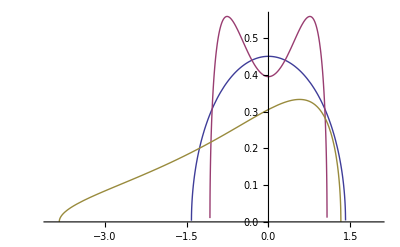

```mathematica
Plot[{emA[x],emB[x],emC[x]},{x,-4,2}]
```

Free probability add A with itself.  Returns another function of the form  SingFun[fun,{1/2,1/2}]

```mathematica
emAA=emA~FreeProbabilityAdd~emA;
```

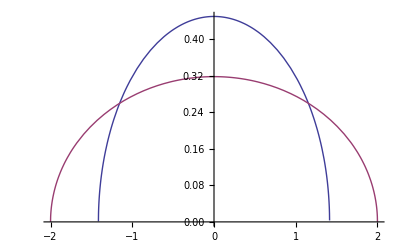

```mathematica
Plot[{emA[x],emAA[x]},{x,-2,2}]
```

We can check the RTransforms agree

```mathematica
RTransform[emAA,.1 I]-2RTransform[emA,.1 I]
```

1.11022×10^-16+8.88178×10^-15 ⅈ

Free probability add A and B (don’t worry about the warnings)

```mathematica
emAB=emA~FreeProbabilityAdd~emB;
```

First::first: {} has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

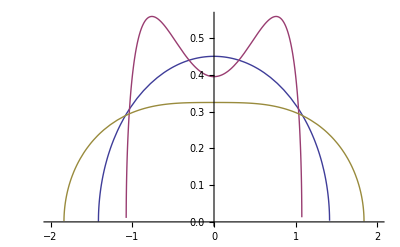

```mathematica
Plot[{emA[x],emB[x],emAB[x]},{x,-2,2}]
```

We can check the RTransforms agree

```mathematica
RTransform[emAB,.1 I]-(RTransform[emA,.1 I]+RTransform[emB,.1 I])
```

-1.51084×10^-13-1.06581×10^-14 ⅈ

Free probability add A and C

```mathematica
emAC=emA~FreeProbabilityAdd~emC;
```

First::first: {} has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

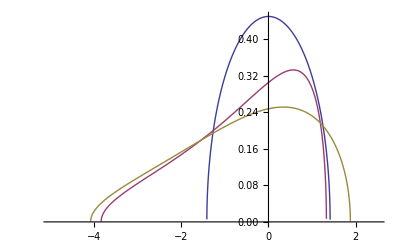

```mathematica
Plot[{emA[x],emC[x],emAC[x]},{x,-5,2.5}]
```

We can check the RTransforms agree

```mathematica
RTransform[emAC,.1 I]-(RTransform[emA,.1 I]+RTransform[emC,.1 I])
```

1.87628×10^-14-2.07834×10^-13 ⅈ